## Constants

```mathematica
(*make sure to run appendix_benchmark_values.nb first*)
```

```mathematica
me=5.11*10^5; (*eV*)
α=1/137;
REarth = 32.322 *10^12; (*eV^-1*)
nF(*[mX_]*):= 2.3*10^(-17)(*0.1*3841/mX*); (*eV^3*)
T= 119(*2.643*); (*eV*)
MEarth = 3.35041*10^(60); (*eV*)
G = 6.70883*10^(-57);(*eV^-2*)
TEarth = 0.345; (*eV*)
(*Particle masses from David's code, in eV*)
mMeeV= currentfoverv*511/1000*10^-3*10^(9);
mHeV = mHGeV[currentfoverv]*10^(9);
mHeeV=4*mHGeV[currentfoverv]*10^(9); 

QX= 2; (*change this to adjust charge of DM*)

(*Free particle densities from David's code, in natural units*)
nFHeeV=currentY (3/10)/(mHeeV*10^(-9))*5/100*7.68*10^(-15);
nFMeeV=currentY (3/10)/(mHeeV*10^(-9))*(5*2)/100*7.68*10^(-15);

(*velocity characteristics of free DM, all in natural units*)
v0HeeVD=SetPrecision[v0kmsHeDisk[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];(*v0 for He in galactic system frame, but not earth frame*)
v0EeVD=SetPrecision[v0kmsEDisk[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];  (*v0 for E in galactic system frame, but not earth frame*)

v0HeeVH=SetPrecision[v0kmsHeHalo[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];(*v0 for He in galactic system frame, but not earth frame*)
v0EeVH=v0kmsEHalo[SetPrecision[currentfoverv,currentY]*(*(30)**)10^5*3.33*10^(-11),20];  (*v0 for E in galactic system frame, but not earth frame*)

(*velocity distributions calculated in David's code*)
fHeDisk[v_]:=(correctf[v/(10^5*3.33*10^(-11))]/.{vescape->vescapehuge, ve->vEarthkmsDisk, v0->v0kmsHeDisk[currentfoverv,currentY]})/(10^5*3.33*10^(-11)); 
fHeHalo[v_]:=(correctf[v/(3.33*10^(-6))]/.{vescape->vescapehuge, ve->vEarthkmsHalo, v0->v0kmsHeHalo[currentfoverv,currentY]})/3.33*10^(-6);
MBNorm[v0_]:=SetPrecision[NIntegrate[v^2 Exp[-3/2 v^2/v0^2],{v,0,10v0}],20];
fH[v_,v0_]:=SetPrecision[ Sqrt[v^2+v2esc[0,5*10^9]]*v^2 Exp[-3/2 v^2/v0^2]/MBNorm[v0],20];
```

InterpolatingFunction::dmval: Input value {9.99×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

## Make Target List

```mathematica
(*Note on conventions: all atoms named by normal abbr. OR if abbr. is 1 letter, by first 2 letters of atom name*)
(*find number density in (eV)^-3 from mass fraction, mass in amu's*)
findnT[massfrac_,amass_]:=massfrac/amass*(5.97217*10^(24))/(1.66054*10^(-27))/(1.4145*10^(41)); 
(*find mass of atom in eV*)
findmT[amass_]:=amass*9.314*10^(8);

(* {Z, massfrac in Earth, mass in amu, number density, mass in eV}*)
OX = {8,.297,15.999,findnT[.297,15.999],findmT[15.999]};
MG = {12,.154,24.305,findnT[.154,24.305],findmT[24.305]};
SI= {14,.161,28.085,findnT[.161,28.085],findmT[28.085]};
FE={26,.319,55.845,findnT[.319,55.845],findmT[55.845]};
AL = {13,.0159,26.982,findnT[.0159,26.982],findmT[26.982]};
CA = {20,.0171,40.078,findnT[.0171,40.078],findmT[40.078]};
NI = {28,.0182,58.693,findnT[.0182,58.693],findmT[58.693]};
HY = {1,.00026,1.008,findnT[.00026,1.008],findmT[1.008]};
SU= {16,.00635,32.06,findnT[.00635,32.06],findmT[32.06]};
CR = {24,.0047,51.996,findnT[.0047,51.996],findmT[51.996]};
NA = {11,.0018,22.990,findnT[.0018,22.990],findmT[22.990]};
CA= {6,.00073,12.011,findnT[.00073,12.011],findmT[12.011]};
PH = {15,.00121,30.974,findnT[.00121,30.974],findmT[30.974]};
```

```mathematica
targList = {OX,MG,SI,FE,AL,CA,NI,HY,SU,CR,NA,CA,PH};
```

## Find Capture Rates (Disk)

```mathematica
v2esc[QEarth_,mX_]:=2*G*MEarth/REarth-1/(2*Pi)*QEarth*QX/(REarth*mX);
```

```mathematica
SSfactorContrib[target_,mX_,ϵ_]:=
(*factor for the contribution of each target to the soft scattering kinetic energy loss*)
If[(4*target[[5]]^2*mX*(T)/((target[[5]]+mX)^2*(me*α)^2))>1,target[[4]]*mX*Pi*α^2*ϵ^2*QX^2*target[[1]]^2/target[[5]]*Log[(4*target[[5]]^2*mX*(T))/((target[[5]]+mX)^2*(me*α)^2)],0];
```

```mathematica
SSfactor[targetList_,mX_,ϵ_]:=Sum[SSfactorContrib[targetList[[i]],mX,ϵ],{i,1,Length[targetList]}];
```

```mathematica
v2cap[target_,mX_,ϵ_,v2esc_]:=
(*from Eq (A.5) in the MDM paper, max velocity of infalling mirror heavy particle at time of Earth entry for soft capture*)
(8*SSfactorContrib[target,mX,ϵ]*REarth/mX^2+v2esc^2)^(1/2);
```

```mathematica
vmin[QEarth_,mX_]:= 
(*for scenarios with -v2esc*)
If[v2esc[QEarth,mX]>0,0,Sqrt[-v2esc[QEarth,mX]]];
```

```mathematica
nFRSoftContrib[target_,mX_,ϵ_,QEarth_]:=
(*contribution from each target to the capture rate per unit volume for soft scatterings*)
nF/(*[mX]*)REarth*NIntegrate[fH[v,v0HeeVD],{v,0(*vmin[QEarth,mX]*),Sqrt[v2cap[target,mX,ϵ,v2esc[QEarth,mX]]-v2esc[QEarth,mX]]}];
```

```mathematica
nFRSoftContrib[OX,5*10^9,10^(-11),0]
```

9.78186×10^-38

```mathematica
nFRSoft[targetList_,mX_, ϵ_, QEarth_]:= Sum[nFRSoftContrib[targetList[[i]],mX,ϵ,QEarth],{i,1,Length[targetList]}];
```

```mathematica
(*hard scattering code. Will get this more organized later*)
reg=10^-6;
vmini[ϵ_,target_]:=SetPrecision[(ϵ^2*4*Pi*α^2*QX^2*REarth*target[[4]]/mHeeV^2)^(1/4),50];
effσvHe[vmin_,vmax_]:=NIntegrate[v*(4Pi*α^2*QX^2)/(mHeeV^2*v^4)*fHeDisk[v],{v,vmin,vmax}]/NIntegrate[fHeDisk[v],{v,0,10*v0HeeVD}];
nFRHardContTest[target_,mX_,eps_,QEarth_]:=(target[[4]]*nFHeeV*eps^2*SetPrecision[effσvHe[vmini[eps,target],Sqrt[(v2esc[QEarth,mX]*(mHeeV+target[[5]])^2/(mHeeV-target[[5]])^2)-v2esc[QEarth,mX]]+reg],50])+(nFHeeV*NIntegrate[fH[v,v0HeeVD],{v,0,vmini[eps,target]}]/REarth);
```

```mathematica
σHT[target_,mX_,ϵ_,v2_]:=(2*Pi*α^2*ϵ^2/(target[[5]]*v2^2)^2)*((target[[5]]+mX)^2/(2*mX^2));
```

```mathematica
nFRHardTest[target_,mX_,ϵ_]:=(nF*ϵ^2*SetPrecision[effσvHe[target,mX,ϵ,vmin[target,mX,ϵ],√(v2esc[0,mX](((mHeeV/10^9+16)/(16-mHeeV/10^9))^2-1))+reg],50])*target[[4]]+nF*NIntegrate[fH[v,v0HeeVD],{v,0,vmin[target,mX,ϵ]}]/REarth
```

```mathematica
p1=LogPlot[nFRSoftContrib[OX,5*10^9,10^logϵ,0]/(5.05*10^(-30)),{logϵ,-12,-9},PlotRange->{{-12,-9},{10^(-14),10^(-5)}},Frame->True,PlotStyle->Blue]//Quiet;
```

```mathematica
p2=LogPlot[1.47*10^9/(4.72*10^8)nFRHardContTest[OX,mHeeV,10^logϵ,0]/(5.05*10^(-30)),{logϵ,-12,-9},PlotRange->{{-12,-9},{10^(-14),10^(-5)}},Frame->True,PlotStyle->Red]//Quiet;
```

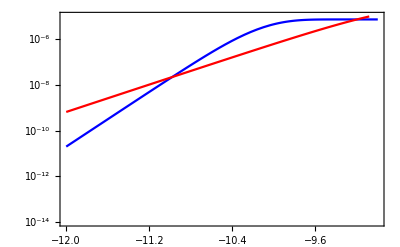

```mathematica
Show[p1,p2]
```

## Find Capture Rates (Halo)

```mathematica
v2esc[QEarth_,mX_]:=2*G*MEarth/REarth-1/(2*Pi)*QEarth*QX/(REarth*mX);
```

```mathematica
SSfactorContrib[target_,mX_,ϵ_]:=
(*factor for the contribution of each target to the soft scattering kinetic energy loss*)
If[(4*target[[5]]^2*mX*(T)/((target[[5]]+mX)^2*(me*α)^2))>1,target[[4]]*mX*Pi*α^2*ϵ^2*QX^2*target[[1]]^2/target[[5]]*Log[(4*target[[5]]^2*mX*(T))/((target[[5]]+mX)^2*(me*α)^2)],0];
```

```mathematica
SSfactor[targetList_,mX_,ϵ_]:=Sum[SSfactorContrib[targetList[[i]],mX,ϵ],{i,1,Length[targetList]}];
```

```mathematica
v2cap[target_,mX_,ϵ_,v2esc_]:=
(*from Eq (A.5) in the MDM paper, max velocity of infalling mirror heavy particle at time of Earth entry for soft capture*)
(8*SSfactorContrib[target,mX,ϵ]*REarth/mX^2+v2esc^2)^(1/2);
```

```mathematica
vmin[QEarth_,mX_]:= 
(*for scenarios with -v2esc*)
If[v2esc[QEarth,mX]>0,0,Sqrt[-v2esc[QEarth,mX]]];
```

```mathematica
nFRSoftContrib[target_,mX_,ϵ_,QEarth_]:=
(*contribution from each target to the capture rate per unit volume for soft scatterings*)
nF/(*[mX]*)REarth*NIntegrate[fH[v,v0HeeVH],{v,0(*vmin[QEarth,mX]*),Sqrt[v2cap[target,mX,ϵ,v2esc[QEarth,mX]]-v2esc[QEarth,mX]]}];
```

```mathematica
nFRSoft[targetList_,mX_, ϵ_, QEarth_]:= Sum[nFRSoftContrib[targetList[[i]],mX,ϵ,QEarth],{i,1,Length[targetList]}];
```

```mathematica
(*hard scattering code. Will get this more organized later*)
reg=10^-6;
vmini[ϵ_,target_]:=SetPrecision[(ϵ^2*4*Pi*α^2*QX^2*REarth*target[[4]]/mHeeV^2)^(1/4),50];
effσvHe[vmin_,vmax_]:=NIntegrate[v*(4Pi*α^2*QX^2)/(mHeeV^2*v^4)*fHeHalo[v],{v,vmin,vmax}]/NIntegrate[fHeHalo[v],{v,0,10*v0HeeVH}];
nFRHardContTest[target_,mX_,eps_,QEarth_]:=(target[[4]]*nFHeeV*eps^2*SetPrecision[effσvHe[vmini[eps,target],Sqrt[(v2esc[QEarth,mX]*(mHeeV+target[[5]])^2/(mHeeV-target[[5]])^2)-v2esc[QEarth,mX]]+reg],50])+(nFHeeV*NIntegrate[fH[v,v0HeeVH],{v,0,vmini[eps,target]}]/REarth);
```

```mathematica
σHT[target_,mX_,ϵ_,v2_]:=(2*Pi*α^2*ϵ^2/(target[[5]]*v2^2)^2)*((target[[5]]+mX)^2/(2*mX^2));
```

```mathematica
nFRHardTest[target_,mX_,ϵ_]:=(nF*ϵ^2*SetPrecision[effσvHe[target,mX,ϵ,vmin[target,mX,ϵ],√(v2esc[0,mX](((mHeeV/10^9+16)/(16-mHeeV/10^9))^2-1))+reg],50])*target[[4]]+nF*NIntegrate[fH[v,v0HeeVH],{v,0,vmin[target,mX,ϵ]}]/REarth
```

```mathematica
p1H=LogPlot[nFRSoftContrib[OX,5*10^9,10^logϵ,0]/(5.05*10^(-30)),{logϵ,-12,-9},PlotRange->{{-12,-9},{10^(-14),10^(-5)}},Frame->True,PlotStyle->Blue]//Quiet;
```

```mathematica
p2H=LogPlot[1.47*10^9/(4.72*10^8)nFRHardContTest[OX,mHeeV,10^logϵ,0]/(5.05*10^(-30)),{logϵ,-12,-9},PlotRange->{{-12,-9},{10^(-14),10^(-5)}},Frame->True,PlotStyle->Red]//Quiet;
```

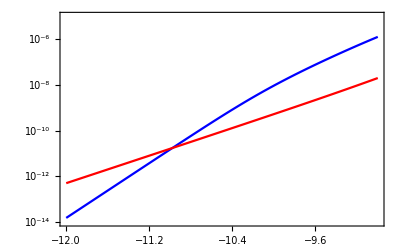

```mathematica
Show[p1H,p2H]
```

## Charge Shielding (Disk)

```mathematica
alphaH = 0;
alphaHe = 2*nFHeeV/(4*nFHeeV+nFMeeV);
alphaE = -nFMeeV/(4*nFHeeV+nFMeeV);
beta0 = 10*10^23/(4*Pi*REarth^3/3)/(4*nFHeeV+nFMeeV);
phiE = beta0/(2*alphaH+3*alphaHe);
```

```mathematica
alphaHe
alphaE
```

0.333333

-0.333333

#### Delta Function Case (Analytic + Numeric)

#### Analytic

```mathematica
(*analytic calculation of screening in delta function case from MDM paper*)
```

```mathematica
A1d=1;
rhoE = beta0/(2*alphaH+3*alphaHe)/5;
```

```mathematica
phiShIntnewA[r_,rMax_]:=((2r^2-rMax^2)-Sqrt[(2r^2-rMax^2)^2+32(r^4-rMax^2r^2)])/(16r^2)/A1d;
RMaxonewA=rMax/.NSolve[{phiShIntnewA[REarth,rMax]==rhoE,rMax>0},rMax][[1]];
phiShnewA[r_]:=Piecewise[{{rhoE,r<=REarth},{phiShIntnewA[r,RMaxonewA],REarth<r<RMaxonewA},{0,r>=RMaxonewA}}]
deltaV=20;
vMax=100;
```

$Aborted

```mathematica
(*make a plot with the analytic delta function ditribution potentials for different values of v_inf*)
A1dList = {{1,Purple},{2,Magenta},{3,Red},{5,Orange},{6,Black},{0.7,Blue},{0.5,Cyan},{0.3,Green},{0.01,Gray},{0.001,Brown}};
PlotList1d=List[];

Do[phiShIntnewA[r_,rMax_]:=((2r^2-rMax^2)-Sqrt[(2r^2-rMax^2)^2+32(r^4-rMax^2r^2)])/(16r^2)/A1dList[[i,1]];
RMaxonewA=rMax/.NSolve[{phiShIntnewA[REarth,rMax]==rhoE,rMax>0},rMax][[1]];
(*Print[RMaxonewA/REarth]*);
Print[RMaxonewA];
phiShnewA[r_]:=Piecewise[{{rhoE,r<=REarth},{phiShIntnewA[r,RMaxonewA],REarth<r<RMaxonewA},{0,r>=RMaxonewA}}];
plotConstVnewA = Plot[rat^2*phiShnewA[REarth rat],
{rat,0.995,1.02},
PlotStyle->A1dList[[i,2]]];
(*Print[(1+A1dList[[i,1]]phiShnewA[REarth]-RMaxonewA^2/REarth^2)];*)
AppendTo[PlotList1d,plotConstVnewA],{i,Length[A1dList]}]
```

3.24651×10^13

3.25811×10^13

3.26711×10^13

3.27765×10^13

3.27936×10^13

3.24251×10^13

3.2397×10^13

3.23678×10^13

3.23236×10^13

3.23222×10^13

```mathematica
REarth
```

3.2322×10^13

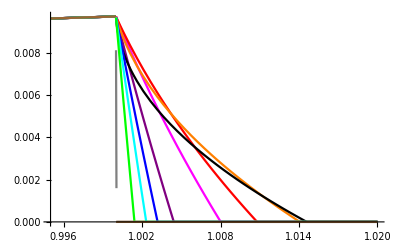

```mathematica
Show[PlotList1d(*,PlotRange->{{0.999,1.00006},{0,0.002}}*)]
```

```mathematica
rhoE
```

0.00971433

#### Numeric

```mathematica
(*numeric calculation of screening in delta function case from MDM paper*)
```

```mathematica
vrat = 1; (*adjust the velocity at infinity, vrat = (2/3 v0^2)/Subscript[v, ∞]^2*)
```

```mathematica
smallrETerm[RMax_,r_,phi_,phiRMax_]:=Piecewise[{{0,r>RMax},{Re[Sqrt[1+phi]Sqrt[1+phi-RMax^2/r^2(1+phiRMax)]],r<=RMax}}];
```

```mathematica
rList=Table[1- 10^-5 i,{i,2000}];
rhoConstVList={};
indexConstV=1;
rhoEarth=beta0/(2*alphaH+3*alphaHe);
While[True,root=phi/.FindRoot[alphaHe*(1-2 *vrat*phi)+alphaE*(1+ vrat*phi-smallrETerm[1,rList[[indexConstV]], vrat*phi,0]),{phi,0.00001,rhoEarth},Method->"Brent"];
 If[root>=rhoEarth-10^(-4),Break[]];AppendTo[rhoConstVList,{rList[[indexConstV]],root}];indexConstV++]
```

```mathematica
rhoEarth
```

0.0485717

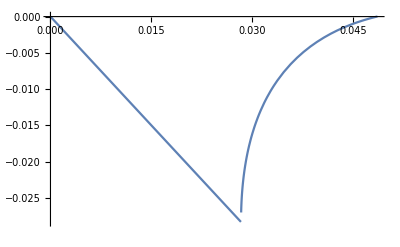

```mathematica
Plot[alphaHe*(1-2 *vrat*phi)+alphaE*(1+ vrat*phi-smallrETerm[1,rList[[indexConstV]], vrat*phi,0]),{phi,0.00001,rhoEarth}]
```

```mathematica
indexConstV
```

1386

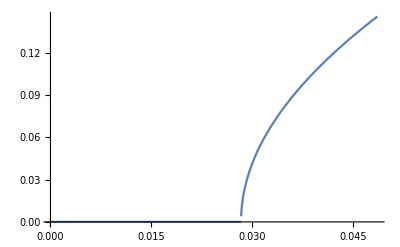

```mathematica
Plot[smallrETerm[1,rList[[indexConstV]], vrat*phi,0],{phi,0.00001,rhoEarth}]
```

```mathematica
phi/.FindRoot[alphaHe*(1-2 *vrat*phi)+alphaE*(1+ vrat*phi-smallrETerm[1,rList[[indexConstV]], vrat*phi,0]),{phi,0.00001,rhoEarth},Method->"Brent"]
```

0.04849

```mathematica
(*RMax initially set to 1, rescale to match REarth*)
rescaleRMaxVConst[elem_]:={elem[[1]]/rhoConstVList[[-1,1]],elem[[2]]};
rescaledrhoConstVList=rescaleRMaxVConst/@rhoConstVList;
```

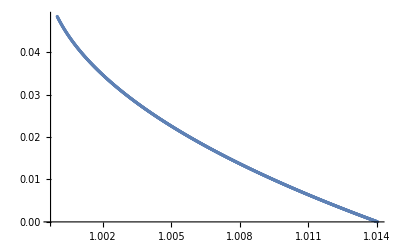

```mathematica
numericalConstV=ListPlot[rescaledrhoConstVList]
```

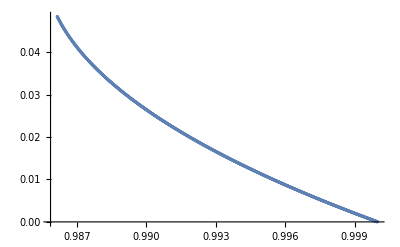

```mathematica
numericalConstVURS = ListPlot[rhoConstVList] (*not rescaled*)
```

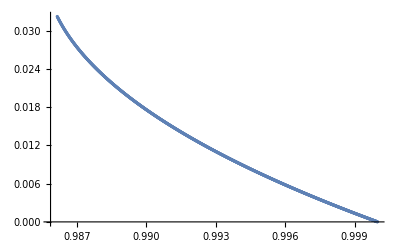

```mathematica
rescaleVURS[elem_]:={elem[[1]],2*elem[[2]]/3};
numericalConstVURSR=ListPlot[Map[rescaleVURS,rhoConstVList]]
```

#### MB Distribution Case

```mathematica
(*create lists for recursion over vinf to find RMax(vinf), also define MB distribution weight factor to match velocities in vInfList*)
vInfList=PowerRange[1/20,4,1+2/10][[9;;]];
MBfactor[i_]:=SetPrecision[ vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2]/MBNorm,20];
MBNorm=SetPrecision[Sum[vInfList[[i]]^2 Exp[-3/2 vInfList[[i]]^2],{i,1,Length[vInfList]}],20];
(*helper functions for the recursion below. *)
```

```mathematica
vInfList
```

{1/20,3/50,9/125,54/625,324/3125,1944/15625,11664/78125,69984/390625,419904/1953125,2519424/9765625,15116544/48828125,90699264/244140625,544195584/1220703125,3265173504/6103515625,19591041024/30517578125,117546246144/152587890625,705277476864/762939453125,4231664861184/3814697265625,25389989167104/19073486328125,152339935002624/95367431640625,914039610015744/476837158203125,5484237660094464/2384185791015625,32905425960566784/11920928955078125,197432555763400704/59604644775390625,1184595334580404224/298023223876953125}

```mathematica
Clear[derivF]
derivF[i_,RMax_,r_,phi_?NumericQ,n_]:=
(*Used to find a good endpoint for solving the F[phi]=0 equation (there can be a superfluous root at higher phi)*)Re[N[((-3+9phi)-Sum[MBfactor[k]/(2 √((vInfList[[k]])^2 + phi)vInfList[[k]]),{k,1,Length[vInfList]}])/n+((MBfactor[i]/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];
(*derivF[i_,RMax_,r_,phi_?NumericQ,n_]:=Re[N[(-4+8phi-14 phi^2)/n+((MBfactor[i]/(2*√(vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]]))vInfList[[i]]))),20]];*)
complexF[i_,RMax_,r_]:=
(*find where the function F[phi] (where we are solving F[phi]=0 to find phi) goes complex, which will cause the root finding protocol to not work well*)
N[RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])-vInfList[[i]]^2,50];
rootF[i_,RMax_,r_,phi_?NumericQ,n_]:=Re[N[(-4phi+4 phi^2-14/3 phi^3)/n+MBfactor[i]/vInfList[[i]] Sqrt[vInfList[[i]]^2+phi-RMax^2/r^2(vInfList[[i]]^2+RMaxList[[i,2]])],50]];
```

```mathematica
(* start of recursion to scan over different r's to find escape potential *)
phiList={{1,0}};
RMaxList={{1,0}};
minPoint =SetPrecision[ 0.9,20];
pointNumber=10000;
Clear[scanPoints];
scanPoints=SetPrecision[Table[1-i(1-minPoint)/pointNumber,{i,pointNumber}],20];
earthFlag=False (*triggers True when escape potential matches Earth potential*);
zoomFlag=False (*triggers True when the recursion zooms in to finer value of the radius*);
(*recursion over different values of v_inf*)
Do[
phiListWorking = {};
delNum=0;
zoomCount=0;
If[earthFlag,Break[]];
If[zoomFlag,Break[]];
Print[j];
(*recursion over different values of r*);
Do[
If[zoomCount>12,zoomFlag=True;Print["You've zoomed in more than 12 times, problem?"];
Break[]];

phiMin=Max[Table[complexF[l,RMaxList[[l,1]],scanPoints[[k]]],{l,j}]]+10^(-15);
Do[If[Sqrt[vInfList[[l]]^2+phiMin-RMaxList[[l,1]]^2/scanPoints[[k]]^2(vInfList[[l]]^2+RMaxList[[l,2]])]<=10^-8,
phiMin+=10^-12],
{l,j}];

phiMax=phi/.FindRoot[Sum[derivF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],{phi,phiMin,0.1},Method->"Brent"];

res=Check[FindRoot[Sum[rootF[i,RMaxList[[i,1]],scanPoints[[k]],phi,j],{i,1,j}],
{phi,phiMin-10^(-12),phiMax},
Method->"Brent",WorkingPrecision->20],$Failed[Evaluate@$MessageList],
FindRoot::bbrac];


If[
FreeQ[res,$Failed](*check whether FindRoot was succesful*),
phiNew=phi/.res;
If[phiNew>2phiE/3,
earthFlag=True;phiList=Join[phiList,phiListWorking];Print["Reached Earth phi"];
Break[]];

(*make updated potential function so far*);
AppendTo[phiListWorking,{scanPoints[[k]],phiNew}];
phiFunc=Interpolation[Join[phiList,phiListWorking]];
delNum+=1;

(*check if we have hit RMax(v_inf)*);
If[phiFunc'[scanPoints[[k]]]*scanPoints[[k]]+2phiFunc[scanPoints[[k]]]+2(vInfList[[j+1]])^2<=0,AppendTo[RMaxList,{scanPoints[[k]],phiNew}];
phiList=Join[phiList,phiListWorking];
scanPoints=Drop[scanPoints,delNum];
pointNumber-=k;
Return[phiList[[-1]]];];,

(*if FindRoot was not succesful, go back a step in r and insert extra points to "fine-grain" your scan over r*)
Print["Zooming In"];
zoomCount+=1;
(*pick extra points to insert*);
If[k==1,insertPoints=Table[RMaxList[[j,1]]-(RMaxList[[j,1]]-scanPoints[[k]])/10 p,{p,0,9}],insertPoints=Table[scanPoints[[k-1]]+(scanPoints[[k]]-scanPoints[[k-1]])/10 p,{p,0,9}]];

scanPoints=Join[scanPoints[[1;;k-1]],insertPoints,scanPoints[[k;;]]];
pointNumber+=10;
delNum+=1
],

{k,10000}],
{j,1,Length[vInfList]-1}];
```

1

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

Interpolation::inhr: Requested order is too high; order has been reduced to {2}.

2

3

4

5

6

$Aborted

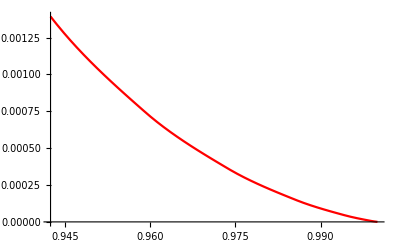

```mathematica
f=Interpolation[phiList];
testCurrent=Plot[f[x],{x,phiList[[-1,1]],1}(*,PlotRange->{{.99903634,1},{0,.011}}*),PlotStyle->Red]
```